```mathematica
steps=6;
job="neutest.q=-1";
Get[job<>"/femoutput.m"];
fdtable=Transpose[Table[Get[job<>"/comp"<>ToString[i]<>".m"];{CompensationCharge,CoreCharge,density,densityScreened,vEff,XC,VZero,vEffAdjusted},{i,0,steps-1}]];
{CompensationCharge,CoreCharge,rho,deltarho,vEff,XC,Vzero,vEffAdjusted}=fdtable;
style={Red,Blue,Red,Blue};
style3={Red,Blue,Green,Red,Blue,Green};
compareplot[pfd_,pfem_,labels_]:=ListPlot[{pfd,pfem,pfd,pfem},Joined->{False,False,True,True},PlotRange->All,PlotStyle->style,AxesLabel->labels,AxesOrigin->{0,0},ImageSize->400]
compareplot3[pfd_,pfem_,patk_,labels_]:=ListPlot[{pfd,pfem,patk,pfd,pfem,patk},Joined->{False,False,False,True,True,True},PlotRange->All,PlotStyle->style3,AxesLabel->labels,AxesOrigin->{0,0},ImageSize->400]
```

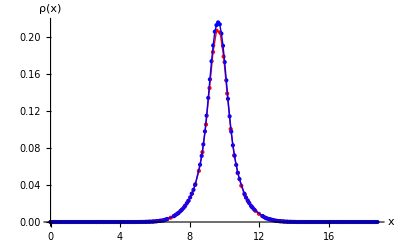
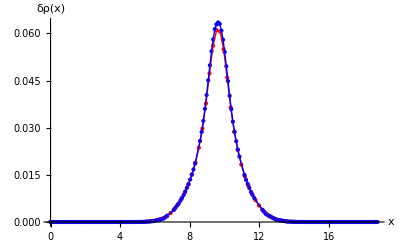
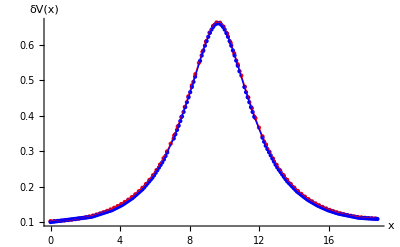
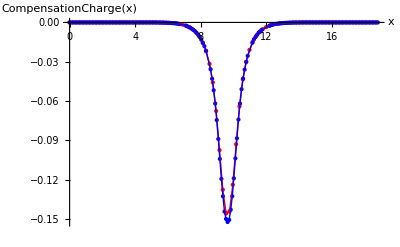
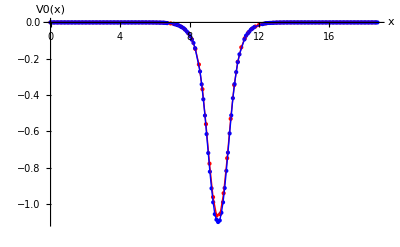
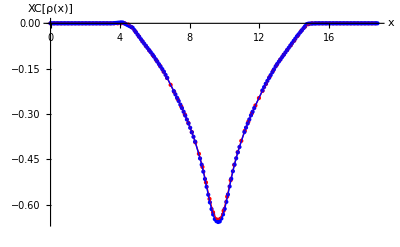
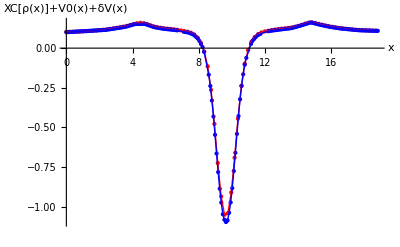

```mathematica
step=6;
plots=compareplot[#[[1,step]],#[[2,step]],#[[3]]]&/@{
{rho,qrho,{x,ρ[x]}},
{deltarho,qdeltarho,{x,δρ[x]}},
{vEff,qvEff,{x,δV[x]}},
{CompensationCharge,qCompensationCharge,{x,"CompensationCharge(x)"}},
{Vzero,qVzero,{x,V0[x]}},
{XC,qXC,{x,"XC"[ρ[x]]}},
{vEffAdjusted,qvEffAdjusted,{x,δV[x]+V0[x]+"XC"[ρ[x]]}}
}
```

```mathematica
Length[rho[[2]]]
```

93

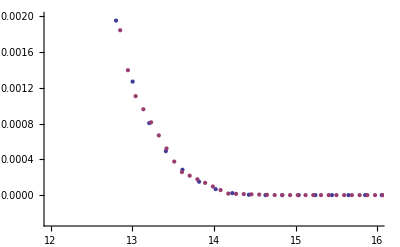

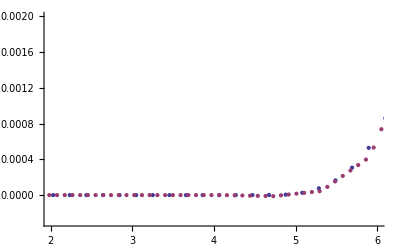

```mathematica
ListPlot[{rho[[step]],qrho[[step]]},PlotRange->{{12,16},{-.0003,.002}}]
ListPlot[{rho[[step]],qrho[[step]]},PlotRange->{{2,6},{-.0003,.002}}]
```

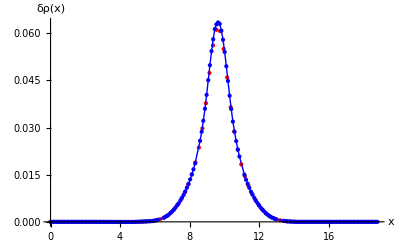

```mathematica
plots[[2]]
```

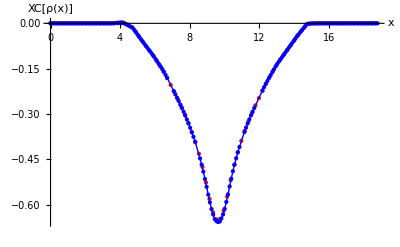

```mathematica
plots[[6]]
```

```mathematica
isneg[{x_,v_}]:={x,If[v<0,-.1,0]};
```

```mathematica
￿
```

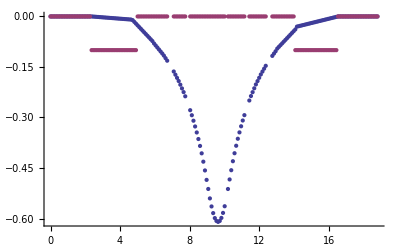

```mathematica
ListPlot[{qXC[[2]],isneg/@qrho[[2]]},Joined->False,PlotRange->All]
```

```mathematica
Min[qrho[[8]]]
```

-0.0000119813

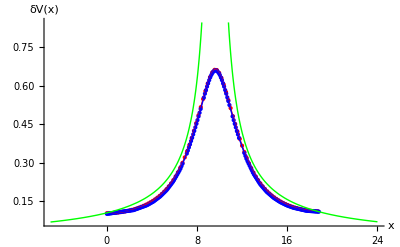

```mathematica
Show[plots[[3]],Plot[1/Abs[9.6-x],{x,-5,24},PlotStyle->{Thick,Green}]]
```

```mathematica
Get["neutest/neutestb-atk.m"];
{bvEff,bdeltarho}={avEff,adeltarho};
Get["neutest/neutest-atk.m"];
```

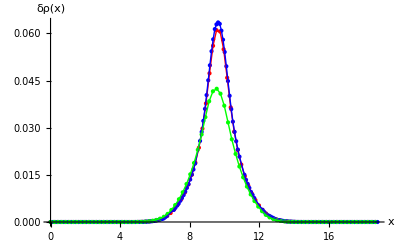

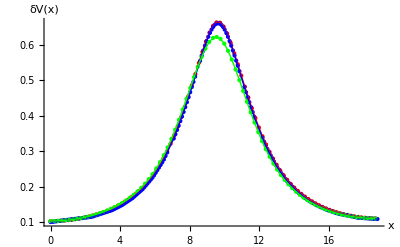

```mathematica
compareplot3[deltarho[[step]],qdeltarho[[step]],adeltarho,{x,δρ[x]}]
compareplot3[vEff[[step]],qvEff[[step]],avEff,{x,δV[x]}]
```

```mathematica
abdiff=Table[{avEff[[i,1]],avEff[[i,2]]-bvEff[[i,2]]},{i,Length[avEff]}];
```

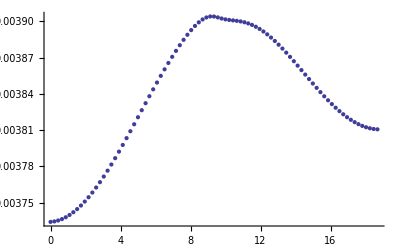

```mathematica
ListPlot[abdiff]
```